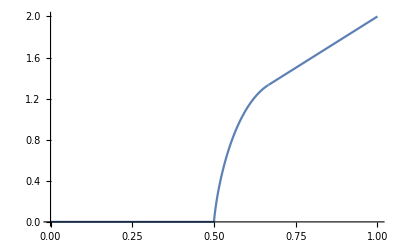

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
DD = 10;
d=DD;
H[a_]:=-a Log[2, a] - (1-a) Log[2, 1-a]; (* Binary entropy function *)
p[a_, eps_]:=p[a, eps]=(1/2)(1-eps)^(1-a)(1+eps)^a; (* The probability without the power d*)
S[d_,a_]:=S[d,a]= Sum[(Binomial[Floor[(1-a) d],t]),{t, Ceiling[a d], Ceiling[(1-a)d], 1} ]; (* Exact sum *)
ExactTermBaseVariance[a_, eps_, d_:DD]:=ExactTermBaseVariance[a, eps, d]=(S[d, a]^2Binomial[d, a d]p[a,eps]^d)^(1/d);
ExactTermVariance[a_, eps_, d_:DD]:=ExactTermVariance[a, eps, d]=(S[d, a]^2Binomial[d, a d]p[a,eps]^d);
SumVariance[eps_, d_:DD]:=SumVariance[eps,d]=Total[ExactTermVariance[#,eps, d]&/@Range[0,d,1/d]]
SumVarianceBase[eps_, d_:DD]:=SumVarianceBase[eps,d]=(SumVariance[eps, d])^(1/d)

Curve[b_]:=Curve[b]=2b H[(1-b)/b]
CurveSlope[x_]:=CurveSlope[x]=D[Curve[a],a]/.{a->x}
Intercept[x_]:=Intercept[x]=x(2-CurveSlope[x])
MyLine[x_, lambda_]:=x CurveSlope[lambda]+Intercept[lambda]
q[eps_,lambda_]:=2^Intercept[lambda](1+eps+(1-eps)2^CurveSlope[lambda])/2



d=10;
Manipulate[
Plot[{
SumVarianceBase[eps, d]
,q[eps,lambda]
}, {eps, 0.6, 1}, PlotLegends->"Expressions", PlotRange->Full]
,{lambda, 1/2+0.00001, 2/3-0.00001}]

Plot[{
If[b≥2/3, 2b, If[b >= 1/2, Curve[b], 0]]
}, {b, 0, 1}, PlotLegends->"Expressions", PlotRange->Full]
```

```mathematica
Log[(1/2)*(33 + Sqrt[65])]
```

```mathematica
N[Log[1/2 (33+√65)]]
```